```mathematica
Plot[Re[ParabolicCylinderD[-1/2,ⅈ x]],{x,0,0.000001}]
```

-Graphics-

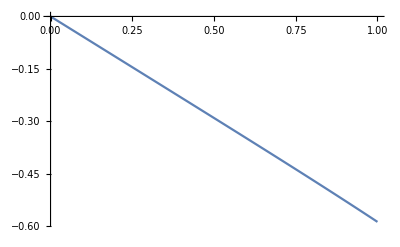

```mathematica
Plot[Im[ParabolicCylinderD[-1/2,ⅈ x]],{x,0,1}]
```

```mathematica
D[ParabolicCylinderD[-1/2,ⅈ x],x]/.x->0
```

-(ⅈ 2^(1/4) √π)/Gamma[1/4]

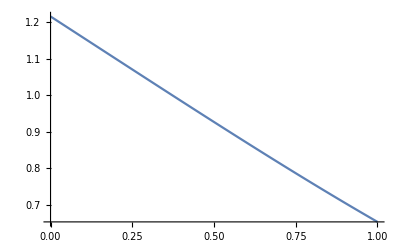

```mathematica
Plot[ParabolicCylinderD[-1/2,x],{x,0,1}]
```

```mathematica
N[D[ParabolicCylinderD[-1/2,x],x]/.x->10000]
```

-4.48114205316005×10^-10857361

```mathematica
D[ParabolicCylinderD[-1/2,ⅈ b x]-ⅈ ParabolicCylinderD[-1/2,b x],x]/.x->0
```

0

```mathematica
N[D[ParabolicCylinderD[-1/2,ⅈ x],x]/.x->10000]
```

3.94490273237324×10^10857363-3.94490273237324×10^10857363 ⅈ

```mathematica
N[(Re[D[ParabolicCylinderD[-1/2,ⅈ √2 a x],x]]ParabolicCylinderD[-1/2,√2 a x]-Re[ParabolicCylinderD[-1/2,ⅈ √2 a x]]D[ParabolicCylinderD[-1/2,√2 a x],x])/.x->20]
```

3.

```mathematica
(ParabolicCylinderD[-1/2,ⅈ √2 a x]-ⅈ ParabolicCylinderD[-1/2,√2 a x])D[ParabolicCylinderD[-1/2,√2 a x],x]-ParabolicCylinderD[-1/2,√2 a x](D[ParabolicCylinderD[-1/2,ⅈ √2 a x]-ⅈ ParabolicCylinderD[-1/2,√2 a x],x])//FullSimplify
```

√2 a (ⅈ HermiteH[-1/2,a x] HermiteH[1/2,ⅈ a x]+HermiteH[-1/2,ⅈ a x] (2 a x HermiteH[-1/2,a x]-HermiteH[1/2,a x]))

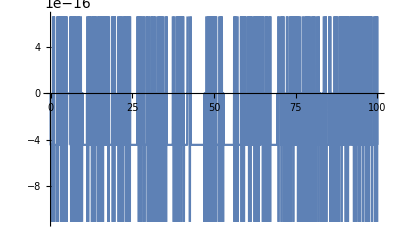

```mathematica
a=3;
Plot[a+Re[√2 a (ⅈ HermiteH[-1/2,a x] HermiteH[1/2,ⅈ a x]+HermiteH[-1/2,ⅈ a x] (2 a x HermiteH[-1/2,a x]-HermiteH[1/2,a x]))],{x,0,100}]
```

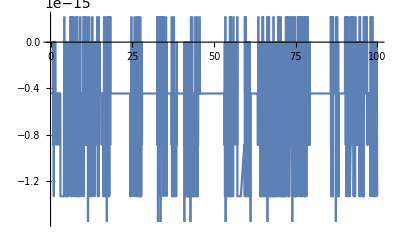

```mathematica
Plot[a-Im[√2 a (ⅈ HermiteH[-1/2,a x] HermiteH[1/2,ⅈ a x]+HermiteH[-1/2,ⅈ a x] (2 a x HermiteH[-1/2,a x]-HermiteH[1/2,a x]))],{x,0,100}]
```

```mathematica
DSolve[f''[x]-x^2 f[x]==0,f[x],x]
```

{{f[x]→C[2] ParabolicCylinderD[-1/2,ⅈ √2 x]+C[1] ParabolicCylinderD[-1/2,√2 x]}}

```mathematica
N[(D[ParabolicCylinderD[-1/2,ⅈ √2 x]-ⅈ ParabolicCylinderD[-1/2,√2 x],x]ParabolicCylinderD[-1/2,√2 x]-(ParabolicCylinderD[-1/2,ⅈ √2 x]-ⅈ ParabolicCylinderD[-1/2,√2 x])D[ParabolicCylinderD[-1/2,√2 x],x])/.x->1000]
```

1.-1. ⅈ

```mathematica
g[x_]:=Quiet[NIntegrate[2Sinc[p x] p/(p^2+1),{p,0,∞}]]
```

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
sol1[x_]:=-ParabolicCylinderD[-1/2,√2 x]NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s],{s,0,x}]-Re[ParabolicCylinderD[-1/2,ⅈ √2 x]]NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s],{s,x,∞}]
```

```mathematica
sol1[2]
```

-0.552522

```mathematica
sol2[x_]:=-1/(1-ⅈ)ParabolicCylinderD[-1/2,√2 x]NIntegrate[(ParabolicCylinderD[-1/2,ⅈ √2 s]-ⅈ ParabolicCylinderD[-1/2,√2 s])s^2 g[s],{s,0,x}]-1/(1-ⅈ)(ParabolicCylinderD[-1/2,ⅈ √2 x]-ⅈ ParabolicCylinderD[-1/2,√2 x])NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s],{s,x,∞}]
```

```mathematica
sol2[2]
```

-0.552522-3.43777×10^-17 ⅈ

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
ND[sol1[x],{x,1},0.0000001]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {4.99984×10^-8}. NIntegrate obtained 1.36811×10^-20 and 3.51474×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.193352}. NIntegrate obtained 0.152696 and 9.07111×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.193356}. NIntegrate obtained 0.0273715 and 8.39168×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-0.00201093

```mathematica
ND[sol1[x],{x,1},10000]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.

```mathematica
ND[sol2[x],{x,1},0.0000001]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {4.99984×10^-8}. NIntegrate obtained 1.36811×10^-20-1.36811×10^-20 ⅈ and 4.97059×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.193352}. NIntegrate obtained 0.152696-0.152696 ⅈ and 1.28285×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.52564}. NIntegrate obtained 0.822491 and 3.112×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-0.00201093-1.94921×10^-14 ⅈ

```mathematica
ND[sol2[x],{x,1},10000]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.+0. ⅈ

```mathematica
ND[sol1[x],{x,2},2]-(2^2)sol1[2]-(2^2)g[2]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.918425}. NIntegrate obtained 4.74508 and 0.000014929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.412566}. NIntegrate obtained 4.50862 and 5.59045×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.480254}. NIntegrate obtained 4.39546 and 6.67429×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.00178332

```mathematica
ND[sol1[x],{x,2},0.00001]-(0.00001^2)sol1[0.00001]-(0.00001^2)g[0.00001]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {6.26938×10^-6}. NIntegrate obtained 9.94833×10^-15 and 3.5947×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.383824}. NIntegrate obtained 0.846531 and 1.62692×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.222653}. NIntegrate obtained 0.152706 and 9.67071×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-0.0647503

```mathematica
ND[sol1[x],{x,2},100]-(100^2)sol1[100]-(100^2)g[100]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {37.6938}. NIntegrate obtained 1.01435×10^306 and 3.11388×10^305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {37.85}. NIntegrate obtained 1.29261×10^306 and 4.67364×10^305 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {37.6762}. NIntegrate obtained 9.48467×10^305 and 4.96637×10^301 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2.0004

```mathematica
ND[sol1[x],{x,2},5]-(5^2)sol1[5]-(5^2)g[5]
```

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.0000540548